```mathematica
alpha:=0
alpha':=0
M:=10^(-3)
m:=10^(-10)
m':=10^(-10)
a:= 10^(-2)
omega:=2*Pi*10
I1 :=M*a^2
p:=M*omega*a^2
mu0:=4*Pi*10^(-7)
A:=mu0*m*m'/(4*Pi*a^3)
g:=9.8
ang2[t_]={theta[t], theta2[t], epsilon[t]}/. NDSolve[{I1*theta2''[t]==I1*omega^2*theta2[t]-omega*p*theta2[t]-3*A*Sin[alpha']*epsilon[t]+A*Sin[alpha'],
M*a^2*epsilon''[t]==-3*A*Sin[alpha']*theta2[t]-9*A*Cos[alpha]*theta[t]+a*M*g,
M*a^2*theta''[t]==M*a^2*omega^2*theta[t]-9*A*Cos[alpha]*epsilon[t]-a*M*g*theta[t]+3*A*Cos[alpha],
theta[0] == 0, theta'[0] == 0,
epsilon[0] == 0, epsilon'[0]==0,
theta2[0] == 0, theta2'[0] == 0},{theta[t], theta2[t], epsilon[t]}, {t, 0, 100}]
```

General::munfl: 1/(4.77651×10^307) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/(5.58715×10^307) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/(6.53535×10^307) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{{InterpolatingFunction[{{0., 100.}}, <>][t],InterpolatingFunction[{{0., 100.}}, <>][t],InterpolatingFunction[{{0., 100.}}, <>][t]}}

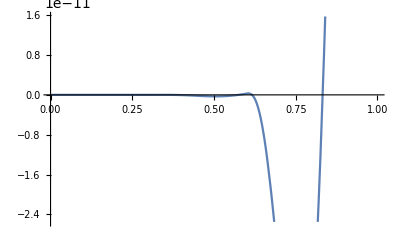

```mathematica
Plot[ang2[t][[1]][[1]], {t, 0,1}]
```

```mathematica
ang2[2][[1]]
```

{-0.00187434,-1.48264×10^-6,1960.}

```mathematica
ang2[2][[1]][[1]]
```

-0.00187434